```mathematica
v1=Table[{Cos[t],Sin[t]},{t,0,2 Pi,2 Pi/5}];
v2=Sin[Pi/10]/Sin[7 Pi/10] v1.RotationMatrix[-Pi/5];
Graphics[GraphicsComplex-[Riffle[v1,v2],Line[Append[Range[1,10],1]]]]
```

```mathematica
Append[Range[1,10],1]
```

{1,2,3,4,5,6,7,8,9,10,1}

```mathematica
Line[Append[Range[1,10],1]]
```

Line[{1,2,3,4,5,6,7,8,9,10,1}]

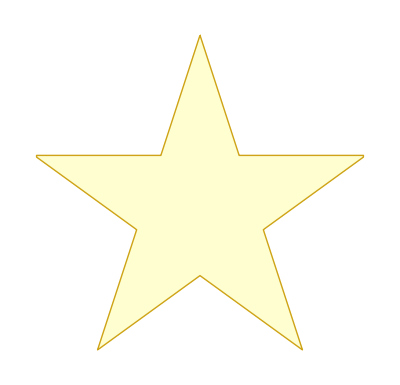

```mathematica
Graphics[{FaceForm[],Sequence@@LaminaData["FilledPentagram","Graphics"]}]
```

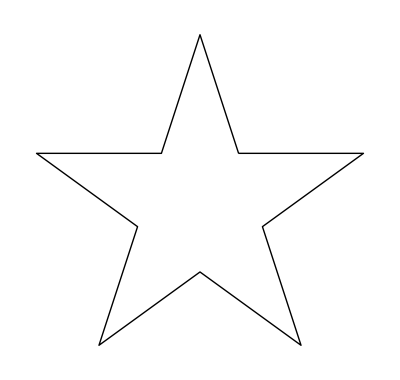

```mathematica
Graphics@Line@AnglePath@Prepend[Riffle[Array[144 °&,5],-72 °],108 °]
```

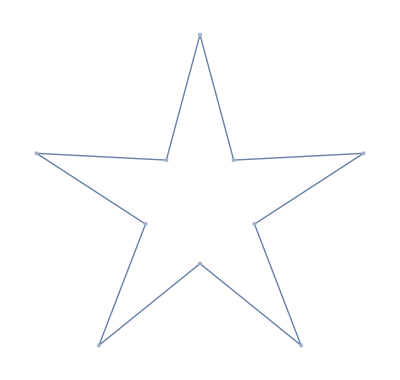

```mathematica
EdgeDelete[NearestNeighborGraph[N@Join[CirclePoints[6,5],inside=RotationMatrix[36 °].#&/@CirclePoints[2,5]],2,EdgeShapeFunction->(Line[#1]&),VertexShapeFunction->None],EdgeList@NearestNeighborGraph[N@inside,2]]
```

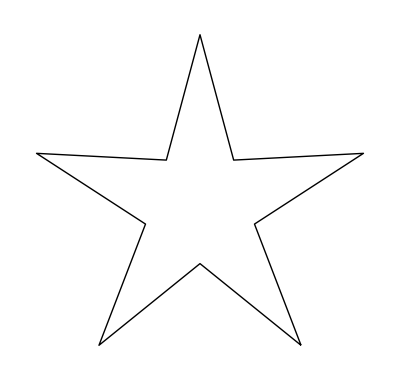

```mathematica
Graphics@Line@point[[Last@FindShortestTour[point=Join[CirclePoints[6,5],inside=RotationMatrix[36 °].#&/@CirclePoints[2,5]]]]]
```

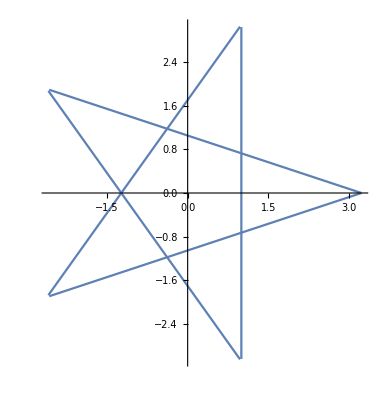

```mathematica
PolarPlot[1/Cos[2 π/5-Mod[θ,4 π/5]],{θ,0,4 π}]
```

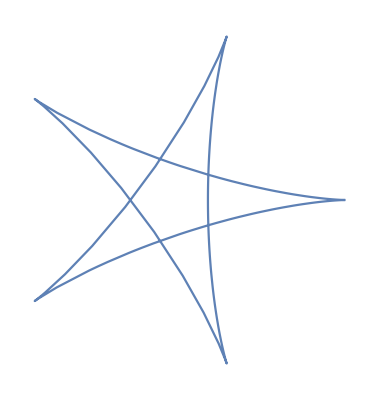

```mathematica
ParametricPlot[{6/25 Cos[t]+4/25 Cos[3/2 t],6/25 Sin[t]-4/25 Sin[3/2 t]},{t,0,4 Pi},Axes->False]
```

## 绘制五角星的一种思路，及扩展

```mathematica
Manipulate[Graphics[Line[AnglePath[
a=(n-2)/n 180°;
b=180°-a;
c=2b;
Prepend[Riffle[Array[c&,n],-b],a]
]]],
{n,5,15,1}]
```

### 当然，也可以简单的使用LaminaData

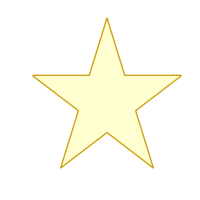

```mathematica
LaminaData["FilledPentagram","Graphics"]
```

## 结束了，谢谢观看。